## Combinatorics

m*n ways of performing both tasks
m+n ways of performing one or the other

### Permutations

ORDERED, no repetitions, no replacement

=(n!)/((n-r)!), n=num of objects, r=how many selected

With like objects: = (n!)/(a!b!c!...),n=num of objects, all others=num of separate like objects

### Combinations

nCr=(n!)/(r!(n-r)!), n=num of objects, r=how many selected

## Discrete Random Variables

order: [weights,values]
(weights must match values)

```mathematica
d=EmpiricalDistribution[{0.05,0.15,0.35,0.25,0.15,0.05}->{100,150,200,250,300,400}]
```

DataDistribution[…]

```mathematica
Probability[X>150,X\[Distributed]d] (*esc dist esc for distr symbol*)
```

0.8

Mean, Variance, Standard Deviation

```mathematica
Mean[d] (*E(X)*)
```

225.

```mathematica
Variance[d](*Var(X)*)
StandardDeviation[d]^2
```

4375.

4375.

```mathematica
StandardDeviation[d]
√Variance[d](*Sd(X)*)
```

66.1438

66.1438

EXAMPLE 2 (for x | 2 | 3 | 4 | 5
Pr(X=x) | 2/27 | 1/6 | 8/27 | 25/54):

```mathematica
(*Mean*)
∑_(x=2)^5 x*x^2/54
2(2/27)+3(1/6)+4(8/27)+5(25/54)
```

112/27

112/27

```mathematica
(*Variance*)
(2^2)(2/27)+(3^2)(1/6)+(4^2)(8/27)+(5^2)(25/54)-(112/27)^2(*sqrt for Standard deviation*)
```

659/729

Median

x | 100 | 150 | 200 | 250 | 300 | 400
p(x) | 0.05 | 0.15 | 0.35 | 0.25 | 0.15 | 0.05

```mathematica
(*Method 1:  Use the table
median of X is ∑Pr(X=x)=0.5*)
0.05+0.15+0.35 (*therefore 200 is median or just use Median[d]*)
```

Conditional

```mathematica
Probability[X≥300\[Conditioned]X>200,X\[Distributed]d]//Rationalize(*esc cond for conditional symbol*)
```

4/9

e.g. q (where goes distr lie?)
	ii.	 Hence find the X values for which 95% of the distribution lies.

2 marks

(*Method which shows full working
μ-2σ≤X≤μ+2σ≈0.95
σ=sd(X)=√(Var(X))*)
{225-2 √4375,225+2 √4375}//N

{92.7124,357.288}

(*Method 2:  Use the defined distribution*)
{Mean[d]-2*StandardDeviation[d],Mean[d]+2*StandardDeviation[d]}

{92.7124,357.288}

Pr(μ-2σ≤X≤μ+2σ)
=Pr(92.71≤X≤357.29)
=Pr(100≤X≤300)    since X can only takes the values in the table from the probability distribtuion of X 
=0.95
Therefore the X values for which 95% of the distribution lies is 100 and 300.

## Binomial Distribution

Tech free Pr(X=x):
n=num trials, p=prob sucess, x=num sucess trials

```mathematica
(n!)/(x!(n-x)!)p^x(1-p)^(n-x)(*x=0,1,2,...n*)
```

Binomial[num tries,probability sucess]

```mathematica
B:=BinomialDistribution[20,0.4]
```

```mathematica
Probability[X==10,X\[Distributed]B]
PDF[B,10]
```

0.117142

0.117142

Pr(X<=x ) can be found using CDF[dist,x], hence Pr(>=10)=1-Pr(X<=9)

```mathematica
Probability[X≥10,X\[Distributed]B]
1-CDF[B,9]
```

0.244663

0.244663

```mathematica
Probability[10≤X≤14,X\[Distributed]B]
Total[PDF[B,{10,11,12,13,14}]]
```

0.243051

0.243051

Conditional:

```mathematica
Probability[X≤10\[Conditioned]X≥5,X\[Distributed]B]
```

0.865632

Min sample size for a probability (n=22)

```mathematica
f[n_]:=Probability[X≥2,X\[Distributed]BinomialDistribution[n,1/5]]
Reduce[f[n]>0.95,n,Integers](*can be unreliable*)
f[22]//N(*CHECK*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n∈ℤ&&n≥22.

0.952038

```mathematica
Table[{n,f[n]},{n,20,30}]//TableForm//N (*reliable, 22 by inspection*)
```

20. | 0.930825
21. | 0.942354
22. | 0.952038
23. | 0.960155
24. | 0.966943
25. | 0.97261
26. | 0.977333
27. | 0.981262
28. | 0.984526
29. | 0.987234
30. | 0.989478

Finding unknown probability

```mathematica
g[p_]:=Probability[X≥34,X\[Distributed]BinomialDistribution[100,p]]
Reduce[g[p]>0.95,p,Reals](*can be unreliable*)
g[0.4155]
g[0.4154](*CHECK ROUNDING*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

BetaRegularized[p,34,67]∈ℝ&&(p<-0.12944||p>0.415454)

0.950095

0.949887

Mean, Variance, Standard Deviation

```mathematica
Mean[B]
20*0.4(*=np*)
```

8.

8.

```mathematica
Variance[B]
20*0.4(1-0.4)(*=np(1-p)*)
StandardDeviation[B]^2
```

4.8

4.8

4.8

```mathematica
StandardDeviation[B]
√Variance[B]
√(20*0.4(1-0.4))
```

2.19089

2.19089

2.19089

Table of values & plotting

```mathematica
Table[{X,PDF[BinomialDistribution[10,0.4],X]},{X,0,10}]//TableForm
```

0 | 0.00604662
1 | 0.0403108
2 | 0.120932
3 | 0.214991
4 | 0.250823
5 | 0.200658
6 | 0.111477
7 | 0.0424673
8 | 0.0106168
9 | 0.00157286
10 | 0.000104858

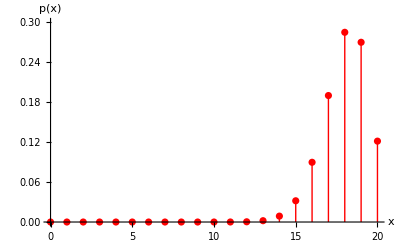

```mathematica
ListPlot[Table[{X,PDF[BinomialDistribution[20,0.9],X]},{X,0,20}],AxesLabel->{x,"p(x)"},
Filling->Axis,PlotStyle->{Directive[Red]},FillingStyle->{Directive[Thick]},PlotRange->{0,0.3}](*THIS IS SCEWED LEFT ALSO NOT CONTINUOUS*)
```

## Continuous Random Variables

Probability (cannot have a Pr X=x)

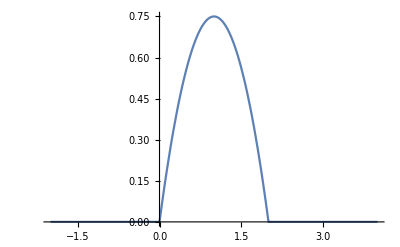

```mathematica
q[x_]:=Piecewise[{{-3/4x(x-2),0≤x≤2}}]
Plot[q[x],{x,-2,4}]
```

```mathematica
dist1=ProbabilityDistribution[q[x],{x,0,2}]
Probability[X≤1/2,X\[Distributed]dist1]
```

ProbabilityDistribution[Piecewise[{{-3/4 (-2+x) x, 0≤x≤2}, {0, True}}],{x,0,2}]

5/32

Conditional:

```mathematica
Probability[X≤1/2\[Conditioned]X≥1/4,X\[Distributed]dist1]
```

29/245

Mean, Variance, Standard Deviation

```mathematica
Mean[dist1]
```

1

```mathematica
Variance[dist1]
StandardDeviation[dist1]^2
```

1/5

1/5

```mathematica
StandardDeviation[dist1]
√Variance[dist1]
```

1/(√5)

1/(√5)

Median

```mathematica
f[x_]:=Piecewise[{{-1/100(x^2-23), 0<=x<=3}, {3/50 x-1/25, 3<x<=5}}]
d:=ProbabilityDistribution[f[x],{x,0,5}]
```

```mathematica
Solve[Integrate[-1/100(x^2-23),{x,0,r}]==1/2&&0<=r<=3,r]//N
Median[d]//N
```

{{r→2.36582}}

2.36582

Inverse probability (esc elem esc, esc reals esc, esc inf esc)

```mathematica
k[x_]:=Piecewise[{{2E^(-2x),x≥0}}]
Assuming[m∈Reals,Solve[Integrate[k[x],{x,-∞,m}]==1/2,m]](*opt 1*)
Assuming[m∈Reals,Solve[Integrate[k[x],{x,m,∞}]==1/2,m]](*opt 2*)
Assuming[m∈Reals,Solve[Integrate[k[x],{x,-∞,m}]==Integrate[k[x],{x,m,∞}],m]](*opt 3*)
```

{{m→Log[2]/2}}

{{m→Log[2]/2}}

{{m→Log[2]/2}}

SPECIAL CASE: median (50th percentile)

```mathematica
dist2=ProbabilityDistribution[k[x],{x,0,∞}]
Median[dist2](*opt 4*)
```

ProbabilityDistribution[Piecewise[{{2 ⅇ^(-2 x), x≥0}, {0, True}}],{x,0,∞}]

Log[2]/2

Check function IS a pdf

```mathematica
Integrate[k[x],{x,-∞,∞}]
Reduce[f[x]<0,x]
```

1

0≤x<1

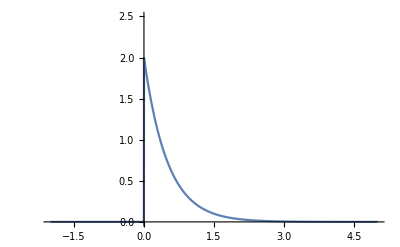

```mathematica
Plot[k[x],{x,-2,5},PlotRange->{0,2.5}]
```

Find the value of a, correct to two decimal places, such that Pr(X ≤ a) = 0.7:

```mathematica
Assuming[0<a<∞,Solve[Integrate[k[x],{x,-∞,a}]==0.7,a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.601986}}

### Pre-knowledge

Piecewise stuff

```mathematica
f[x_]:=Piecewise[{{x^2+1,x<-1},{x-1,x≥0}}]
```

```mathematica
f[3]
f[-0.5] (*outside domain in mathematica but 0 in actual*)
```

2

0

```mathematica
DownValues[f](*rule*)
```

{HoldPattern[f[x_]]:>Piecewise[{{x^2+1, x<-1}, {x-1, x≥0}}]}

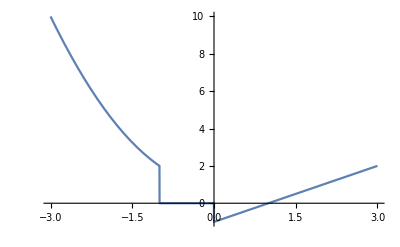

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
g[x_]:=Piecewise[{{x-1,x<0},{Sqrt[x],x≥0}}]/;-3≤x≤3
```

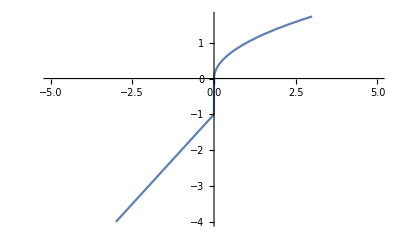

```mathematica
Plot[g[x],{x,-5,5}]
```

Integrals stuff

```mathematica
Integrate[1/(x-1)^3,{x,2,4}]
```

4/9

```mathematica
NIntegrate[Log[x]Exp[-x^2],{x,1,∞}]
```

0.0358827

```mathematica
Assuming[a>2,Solve[Integrate[2/3(x^2-1)^(3/2),{x,2,a}]==4,a,Reals]]//N(*solving for an unknown terminal*)
```

{{a→2.63833}}

## Normal Distribution

Probability:

```mathematica
NO:=NormalDistribution[176,7]
Probability[176<X<185,X\[Distributed]NO]//N (*NProbability faster*)
```

0.400729

Conditional

```mathematica
NProbability[X>174\[Conditioned]X>170,X\[Distributed]NO]
```

0.761454

Inverse normal calculation (calculating a quantile)

Example 3: Let X ~ Normal(μ = 176, σ = 7). Find the value of w such that Pr(X < w) = 0.1265.

```mathematica
NO2:=NormalDistribution[65,5]
NSolve[Probability[70-a<X<50+a,X\[Distributed]NO2]==1/2,a,Reals]//FullSimplify (*opt 1*)
```

{{a→15.2527}}

```mathematica
FindInstance[Probability[70-a<X<50+a,X\[Distributed]NO2]==1/2,a,Reals]//N (*opt 2*)
```

{{a→15.2527}}

```mathematica
NSolve[Probability[70-a<X<50+a,X\[Distributed]NO2]==1/2,a,Reals] (*opt 3*)
```

{{a→15.2527}}

NOT RECOMMENDED (methods 2 & 3)
Method 2:  Use Quantile[dist,q] (where q is the area to the left of the quantile).

Example 2: Let X ~ Normal(μ = 176, σ = 7). Find the value of w such that Pr(X > w) = 0.15.

```mathematica
Quantile[NormalDistribution[176,7],1-0.15]
```

183.255

Method 3: Use InverseCDF[dist,q] where q is the area to the left of the quantile).

Example 2: Let X ~ Normal(μ = 176, σ = 7). Find the value of w such that Pr(X > w) = 0.15.

```mathematica
InverseCDF[NormalDistribution[176,7],1-0.15]
```

183.255

Finding an unknown mean/standard deviation from given probabilities

Method 1: Use Mathematica directly (Note: include the picture in Method 2 if working is required).

```mathematica
NSolve[{Probability[X<-2,X\[Distributed]NormalDistribution[m,s]]==0.4,
Probability[X>-1,X\[Distributed]NormalDistribution[m,s]]==0.3},{m,s}]
```

{{m→-1.67426,s→1.28576}}

Method 2: Use the transformation relationship Z=(X-μ_X)/σ_X.
Note: This method is inefficient in a CAS assessment but will be required if the question asks to express the given probability data as equations in terms of the mean and standard deviation.

-Graphics-

-Graphics-

Getting the values of Z_(X=-1)=b and Z_(X=-2)=a is an ‘inverse normal’ problem:

```mathematica
NSolve[Probability[Z≤a,Z\[Distributed]NormalDistribution[0,1]]==0.4,a]
NSolve[Probability[Z≥b,Z\[Distributed]NormalDistribution[0,1]]==0.3,b]
```

{{a→-0.253347}}

{{b→0.524401}}

Therefore μ_X and σ_X can be found by solving the following pair of simultaneous equations:

-Graphics-

```mathematica
NSolve[{-0.2533471031357998==(-2-m)/s,0.5244005127080408==(-1-m)/s},{m,s},Reals]
```

{{m→-1.67426,s→1.28576}}

Solving equations with two normal random variables

Example 4:
-Graphics-

Method 1: Note that working might be required (include the picture in Method 3 if working is required)

```mathematica
Solve[Probability[W<a,W\[Distributed]NormalDistribution[3/2,4/10]]
==Probability[Z>a/3,Z\[Distributed]NormalDistribution[0,1]],a,Reals]//FullSimplify (*fractions give fraction result AND REALS DOMAIN ESSENTIAL*)
```

{{a→45/34}}

Method 2: Note that working might be required (include the picture in Method 3 if working is required)

```mathematica
FindRoot[Probability[W<a,W\[Distributed]NormalDistribution[1.5,0.4]]
==Probability[Z>a/3,Z\[Distributed]NormalDistribution[0,1]],{a,0}]
```

{a→1.32353}

Method 3 (‘by hand’):

-Graphics-

```mathematica
Solve[(a-(15/10))/(4/10)==-a/3,a,Reals]
```

{{a→45/34}}

Algebra :

-Graphics-

## Sampling

## Custom Functions

```mathematica
ncr[n_,r_]:=(n!)/(r!(n-r)!)
```

```mathematica
npr[n_,r_]:=(n!)/((n-r)!)
```

```mathematica
pbin[n_,p_,x_]:=(n!)/(x!(n-x)!)p^x(1-p)^(n-x)
```

```mathematica
NormalCDF[x_,m_,s_]:=CDF[NormalDistribution[m,s],x]
```

```mathematica
B[n_,p_]:=BinomialDistribution[n,p]
```

```mathematica
No[m_,s_]:=NormalDistribution[m,s]
```

```mathematica
P[f_,{x_,min_,max_}]:=ProbabilityDistribution[f,{x,min,max}]
```

```mathematica
Pr[event_,cond_]:=Probability[event,cond]
```

```mathematica
PNormal[dist_,{x_,min_,max_}]:=Plot[PDF[dist,x],{x,min,max}]
```

```mathematica
PDiscrete[dist_,{x_,min_,max_}]:=ListPlot[Table[{x,PDF[dist,x]},{x,min,max}],Filling->Axis,PlotStyle->{Directive[Red]},FillingStyle->{Directive[Thick]}]
```

```mathematica
CBinomial[dist_,{x_,min_,max_}]:=Table[{x,dist},{n,min,max}]//TableForm//N
```

```mathematica
MSV[dist_]:={"Mean"->Mean[dist],"Standard Deviation"->StandardDeviation[dist],"Variance"->Variance[dist]}
```

```mathematica
(*a bit dodgy but takes in x and rule for x that gives prob then the domain in a table then returns the empirical distr*)
CustomEmpiricalDistribution[table_List]:=Module[{data,probabilities,empiricalDist},data=table[[All,1]];probabilities=table[[All,2]];empiricalDist=EmpiricalDistribution[WeightedData[data,probabilities]];
Return[empiricalDist];]

table=Table[{x,x^2/54},{x,2,5}];
empiricalDist=CustomEmpiricalDistribution[table];
Probability[X>=4,X\[Distributed]empiricalDist]
```